```mathematica
Needs["IntegerSequences`"]
```

## values of a sequence

```mathematica
ruler=RegularSequence[{1,0},{{{0,0},{-1,1}},{{0,1},{-1,2}}},{0,1}];
```

```mathematica
Table[ruler[n],{n,0,15}]
```

{0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,4}

## closure properties

```mathematica
SternBrocot/@Range[0,15]
```

{0,1,1,2,1,3,2,3,1,4,3,5,2,5,3,4}

```mathematica
Table[SternBrocot[n]/SternBrocot[n+1],{n,0,15}]
```

{0,1,1/2,2,1/3,3/2,2/3,3,1/4,4/3,3/5,5/2,2/5,5/3,3/4,4}

```mathematica
RegularSequenceReduce[2 SternBrocot[n]+ThueMorse[n]ruler[n],n]
```

RegularSequence[{1,0,1,0,0,0},{{{1,0,0,0,0,0},{1,1,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,-1,0,1,0},{0,0,0,-1,0,1}},{{0,1,0,0,0,0},{-1,2,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,-1,0,2},{0,0,-1,0,2,0}}},{0,2,0,0,0,1},2][n]

```mathematica
RegularSequenceMatrixForm[%]
```

RegularSequence[{1,0,1,0,0,0},{(1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0
-1 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 2
0 | 0 | -1 | 0 | 2 | 0)},{0,2,0,0,0,1},2][n]

## guessing

### number of 1s in binary

```mathematica
terms=Table[DigitCount[n,2,1],{n,0,50}]
```

{0,1,1,2,1,2,2,3,1,2,2,3,2,3,3,4,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,1,2,2,3,2,3,3,4,2,3,3,4,3,4,4,5,2,3,3}

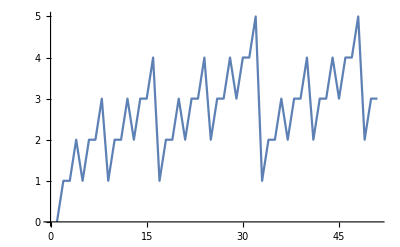

```mathematica
ListLinePlot[terms]
```

```mathematica
FindRegularSequenceFunction[terms,2]//RegularSequenceMatrixForm
```

RegularSequence[{1,0},{(1 | 0
0 | 1),(0 | 1
-1 | 2)},{0,1},2]

Or guess a recurrence:

```mathematica
FindRegularSequenceRecurrence[terms,2,s[n]]//Column
```

s[2 n]==s[n]
s[1+4 n]==s[1+2 n]
s[3+4 n]==-s[n]+2 s[1+2 n]
s[0]==0
s[1]==1

### multidimensional sequences

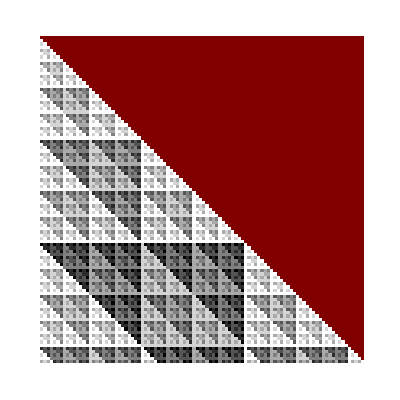

```mathematica
ArrayPlot[array=Table[IntegerExponent[Binomial[n,m],2],{n,0,100},{m,0,100}]]
```

```mathematica
FindRegularSequenceFunction[array/.∞->infinity,2]//RegularSequenceMatrixForm
```

RegularSequence[{1,0,0,0},{{(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | -1 | 2 | 0
0 | 0 | 0 | 1),(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | -1 | 2 | 0
0 | 0 | 1 | 0)},{(1 | 0 | 0 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 2
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | -1 | 2 | 0
0 | 0 | 0 | 1)}},{0,infinity,infinity,1},{2,2}]

### extremal words

Lexicographically least sequence avoiding squares:

```mathematica
Table[ruler[n],{n,0,15}]
```

{0,1,0,2,0,1,0,3,0,1,0,2,0,1,0,4}

```mathematica
0,1,0
```

Lexicographically least sequence avoiding 3/2-powers:

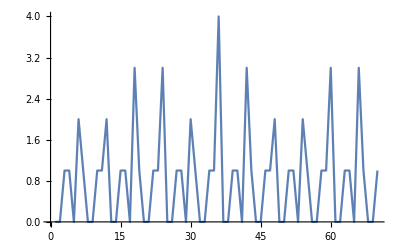

```mathematica
ListLinePlot[{0,0,1,1,0,2,1,0,0,1,1,2,0,0,1,1,0,3,1,0,0,1,1,3,0,0,1,1,0,2,1,0,0,1,1,4,0,0,1,1,0,3,1,0,0,1,1,2,0,0,1,1,0,2,1,0,0,1,1,3,0,0,1,1,0,3,1,0,0,1},PlotRange->All]
```

```mathematica
FindRegularSequenceFunction[{0,0,1,1,0,2,1,0,0,1,1,2,0,0,1,1,0,3,1,0,0,1,1,3,0,0,1,1,0,2,1,0,0,1,1,4,0,0,1,1,0,3,1,0,0,1,1,2,0,0,1,1,0,2,1,0,0,1,1,3,0,0,1,1,0,3,1,0,0,1},6]
```

RegularSequence[{1,0,0},{{{0,1,0},{0,0,0},{0,1,1}},{{0,0,0},{0,1,1},{0,0,0}},{{0,0,1},{0,0,0},{0,1,1}},{{0,1,1},{0,1,1},{0,0,0}},{{0,1,0},{0,0,0},{0,1,1}},{{1,2,2},{0,1,1},{0,0,0}}},{0,0,1},6]

```mathematica
RegularSequenceMatrixForm[%]
```

RegularSequence[{1,0,0},{(0 | 1 | 0
0 | 0 | 0
0 | 1 | 1),(0 | 0 | 0
0 | 1 | 1
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 1 | 1),(0 | 1 | 1
0 | 1 | 1
0 | 0 | 0),(0 | 1 | 0
0 | 0 | 0
0 | 1 | 1),(1 | 2 | 2
0 | 1 | 1
0 | 0 | 0)},{0,0,1},6]

Theorem (Rowland–Shallit 2012).
The lexicographically least 3/2-power-free sequence is 6-regular.

Theorems (Pudwell–Rowland 2018).
The lexicographically least 5/3-power-free sequence is 7-regular.
The lexicographically least 8/5-power-free sequence is 733-regular.
The lexicographically least 7/4-power-free sequence is 50847-regular.
etc. etc.

## computing automata for sequences modulo p^α

### Catalan numbers modulo 3

```mathematica
Table[Mod[CatalanNumber[n],3],{n,0,15}]
```

{1,1,2,2,2,0,0,0,2,2,2,1,1,1,0,0}

```mathematica
AutomaticSequenceReduce[Mod[CatalanNumber[n],3],n]
```

AutomaticSequence[Automaton[{{1→2,0},{1→2,1},{1→3,2},{2→2,0},{2→4,1},{2→5,2},{3→4,0},{3→5,1},{3→3,2},{4→4,0},{4→2,1},{4→5,2},{5→5,0},{5→5,1},{5→5,2}},1,{1→1,2→1,3→2,4→2,5→0},InputAlphabet→{0,1,2}]][n]

```mathematica
AutomatonGraph[AutomaticSequenceAutomaton[%]]
```

-Graphics-

```mathematica
VertexCount[%]
```

6

### diagonal of a rational power series

```mathematica
AutomaticSequenceReduce[Mod[DiagonalSequence[(1-x)/(1-(1+x)^2 y),{x,y}][n],4],n]
```

AutomaticSequence[Automaton[{{1→2,0},{1→1,1},{2→2,0},{2→3,1},{3→3,0},{3→4,1},{4→4,0},{4→4,1}},1,{1→1,2→1,3→2,4→0},InputAlphabet→{0,1}]][n]

```mathematica
AutomatonGraph[AutomaticSequenceAutomaton[%]]
```

-Graphics-

### Motzkin numbers modulo 8

```mathematica
Table[MotzkinNumber[n],{n,0,10}]
```

{1,1,2,4,9,21,51,127,323,835,2188}

What values does the sequence of Motzkin numbers take modulo 8?

```mathematica
AutomatonGraph[automaton=AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[MotzkinNumber[n],8],n]],VertexSize->.5]
```

-Graphics-

```mathematica
Sort[AutomatonOutputAlphabet[automaton]]
```

{1,2,3,4,5,6,7}

### Motzkin numbers modulo 13^2

Theorem (Rowland–Yassawi 2015).
No Motzkin number is divisible by 13^2.

### Apéry numbers modulo 16

```mathematica
Table[AperyNumber[n],{n,0,10}]
```

{1,5,73,1445,33001,819005,21460825,584307365,16367912425,468690849005,13657436403073}

Gessel (1982) proved that the Apéry numbers are periodic modulo 8:

```mathematica
Table[Mod[AperyNumber[n],8],{n,0,15}]
```

{1,5,1,5,1,5,1,5,1,5,1,5,1,5,1,5}

He asked whether they are periodic modulo 16.

```mathematica
Table[Mod[AperyNumber[n],16],{n,0,15}]
```

{1,5,9,5,9,13,9,5,9,13,1,13,9,13,9,5}

```mathematica
AutomatonGraph[automaton=AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],16],n,Method->"Diagonal",Monitor->True]],VertexSize->.4]
```

-Graphics-

Theorem (Rowland–Yassawi 2015).
The Apéry numbers are not eventually periodic modulo 16.